Вариант 7 Логаш Полина

1.1) Задаём функцию и начальные данные:

```mathematica
f[x_]=Tan[x]^2;
X={0,π/6,π/4,π/3,π/12};
n=Length[X]-1;
Do[{Subscript[x, i]=X[[i+1]],Subscript[f, i]=f[Subscript[x, i]]},{i,0,n}]
```

1.2) Строим алгебраический интерполяционный многочлен:

```mathematica
koef=Solve[Table[Subscript[a, 0]+∑_(k=1)^n Subscript[a, k] Subscript[x, j]^k==Subscript[f, j],{j,0,n}],{}][[1]]
P[x_]=∑_(k=0)^n Subscript[a, k] x^k//.koef//Expand
```

{a_0→0,a_1→-(-331+192 √3)/π,a_2→(6 (-713+416 √3))/π^2,a_3→-(432 (-41+24 √3))/π^3,a_4→(864 (-27+16 √3))/π^4}

(331 x)/π-(192 √3 x)/π-(4278 x^2)/π^2+(2496 √3 x^2)/π^2+(17712 x^3)/π^3-(10368 √3 x^3)/π^3-(23328 x^4)/π^4+(13824 √3 x^4)/π^4

2.3) Строим алгебраический интерполяционный многочлен с помощью функции InterpolatingPolynomial:

```mathematica
Tbl=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
P1[x_]=InterpolatingPolynomial[Tbl,x]//Expand
```

(331 x)/π-(192 √3 x)/π-(4278 x^2)/π^2+(2496 √3 x^2)/π^2+(17712 x^3)/π^3-(10368 √3 x^3)/π^3-(23328 x^4)/π^4+(13824 √3 x^4)/π^4

2.4) Сраниваем интерполяционные многочлены:

```mathematica
P[x]==P1[x]
```

True

2.5) Проверяем выполнение интерполяционных условий:

```mathematica
Table[P[Subscript[x, i] ]==Subscript[f, i],{i,0,n}]
```

{True,True,True,True,True}

3.6) Изображаем исходную систему точек, заданную функцию и полученный
интерполяционный многочлен в одной системе координат:

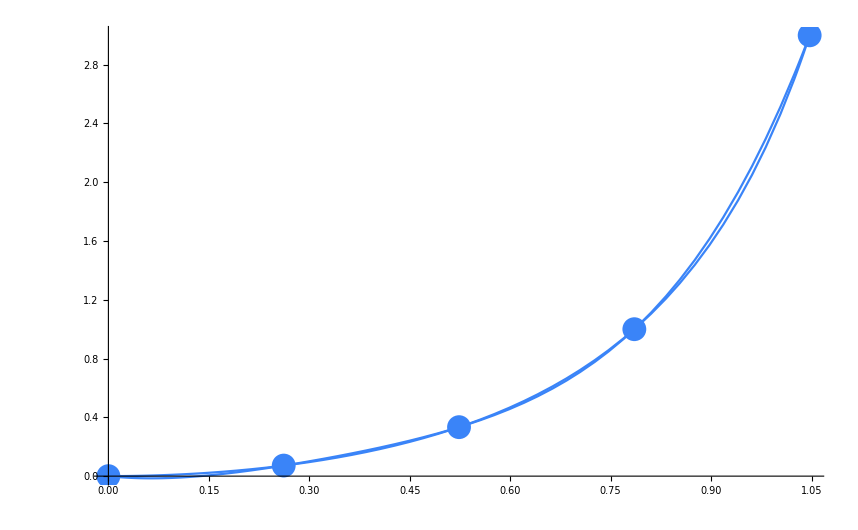

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Min[X],Max[X]}];
Gr3=Plot[f[x],{x,Min[X],Max[X]}];
Show[Gr1,Gr2,Gr3]
```

4.7) Находим приближенное значение f(x) при указанном аргументе:

```mathematica
SuperStar[x]=π/9;
P[SuperStar[x]]
```

127/27-640/(81 √3)

4.8)  Приближенное значение сравниваем с точным значением функции (находим абсолютную и
относительную погрешность приближения):

```mathematica
A=N[Abs[f[SuperStar[x]]-P[SuperStar[x]]],2]
B=N[A/(P[SuperStar[x]]//Abs)*100,2]
```

0.0094

6.7